# octet.experiment.data.raw.nb

```mathematica
NotebookFileName[]
```

C:\Users\Tom\Desktop\octet.paper.chpt.ed2\octet.experiment.data.raw.nb

```mathematica
SetDirectory["C:\\Users\\Tom\\Desktop"]
```

C:\Users\Tom\Desktop

```mathematica
Directory[]
```

C:\Users\Tom\Desktop

## initial

```mathematica
Needs["ErrorBarPlots`"]
```

## nucleon.ge.total

```mathematica
FileNameJoin[{Directory[],"nucleon.ge.total.csv"}]
```

C:\Users\Tom\Desktop\nucleon.ge.total.csv

```mathematica
te`data=Import[FileNameJoin[{Directory[],"nucleon.ge.total.csv"}], "Data"]
```

Import::nffil: 在 Import 中未找到文件.

$Failed

```mathematica
te`data//Dimensions
```

{}

```mathematica
ListPlot[te`data]
```

General::sfunc: {{Identity,Identity},{Identity,Identity}} 不是一个有效的尺度函数.

ListPlot[$Failed]

```mathematica
te`data2=SortBy[te`data, First]
```

SortBy::normal: SortBy[$Failed,First] 中的位置 1 处应该是非原子表达式.

SortBy[$Failed,First]

```mathematica
te`data3=Table[
{
{Mean[te`data2⟦ii;;ii+1,1⟧],
1/4(2*Median[te`data2⟦ii;;ii+2,2⟧]+Max[te`data2⟦ii;;ii+2,2⟧]+Min[te`data2⟦ii;;ii+2,2⟧])
},
1/2(Max[te`data2⟦ii;;ii+2,2⟧]-Min[te`data2⟦ii;;ii+2,2⟧])
}
,{ii,1,Length[te`data2],3}
]
```

Part::partd: 部分指定 SortBy[$Failed,First]⟦1;;2,1⟧ 比对象深度更长.

Part::take: 无法在 SortBy[$Failed,First] 中提取位置 1 至 3.

General::stop: 在本次计算中，Part::take 的进一步输出将被抑制.

{{{Mean[SortBy[$Failed,First]⟦1;;2,1⟧],1/4 (2 Median[SortBy[$Failed,First]⟦1;;3,2⟧]+2 SortBy[$Failed,First]⟦1;;3,2⟧)},0}}

```mathematica
te`data4=MapAt[ErrorBar,te`data3,{;;,2}]
```

{{{Mean[SortBy[$Failed,First]⟦1;;2,1⟧],1/4 (2 Median[SortBy[$Failed,First]⟦1;;3,2⟧]+2 SortBy[$Failed,First]⟦1;;3,2⟧)},ErrorBar[0]}}

```mathematica
ErrorListPlot[
te`data4,
AxesOrigin->{0,0},
PlotRange->{Full,Full},
PlotRangePadding->{Automatic,Scaled[.3]},
ImageSize->Scaled[0.4],
AspectRatio->1/GoldenRatio,
Frame->True
]
```

-Graphics-

## nucleon.ge.light

```mathematica
SetDirectory["C:\\Users\\Tom\\Desktop"];
```

```mathematica
FileNameJoin[{Directory[],"nucleon.ge.light.csv"}]
```

C:\Users\Tom\Desktop\nucleon.ge.light.csv

```mathematica
te`data=Import[FileNameJoin[{Directory[],"nucleon.ge.light.csv"}], "Data"]
```

{{0,-4.53322×10^-7},{0,0.000111435},{0,-0.000130989},{0.0499448,0.00143312},{0.0499448,0.0034471},{0.0503867,0.00258927},{0.0998895,0.00245643},{0.100331,0.00499254},{0.100331,0.00389231},{0.149834,0.00448673},{0.149834,0.00278976},{0.150276,0.00582937},{0.199779,0.00634921},{0.200221,0.00457762},{0.200221,0.00248905},{0.250166,0.00483637},{0.250166,0.00677576},{0.250166,0.00254266},{0.30011,0.00500187},{0.30011,0.0070718},{0.30011,0.00259628},{0.350055,0.00464523},{0.350055,0.00703218},{0.350055,0.00188532},{0.399558,0.0077012},{0.4,0.0047175},{0.4,0.0013795},{0.449503,0.00870586},{0.449945,0.0053119},{0.449945,0.00156365},{0.49989,0.00463825},{0.49989,0.00857298},{0.49989,0.00036785}}

```mathematica
te`data//Dimensions
```

{33,2}

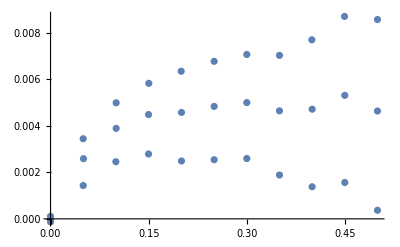

```mathematica
ListPlot[te`data]
```

```mathematica
te`data2=SortBy[te`data, First]
```

{{0,-0.000130989},{0,-4.53322×10^-7},{0,0.000111435},{0.0499448,0.00143312},{0.0499448,0.0034471},{0.0503867,0.00258927},{0.0998895,0.00245643},{0.100331,0.00499254},{0.100331,0.00389231},{0.149834,0.00278976},{0.149834,0.00448673},{0.150276,0.00582937},{0.199779,0.00634921},{0.200221,0.00248905},{0.200221,0.00457762},{0.250166,0.00483637},{0.250166,0.00254266},{0.250166,0.00677576},{0.30011,0.00500187},{0.30011,0.00259628},{0.30011,0.0070718},{0.350055,0.00188532},{0.350055,0.00464523},{0.350055,0.00703218},{0.399558,0.0077012},{0.4,0.0013795},{0.4,0.0047175},{0.449503,0.00870586},{0.449945,0.00156365},{0.449945,0.0053119},{0.49989,0.00463825},{0.49989,0.00036785},{0.49989,0.00857298}}

gather into positive and negative

```mathematica
te`data3=GatherBy[te`data2,(##⟦2⟧>0)&]
```

{{{0,-0.000130989},{0,-4.53322×10^-7}},{{0,0.000111435},{0.0499448,0.00143312},{0.0499448,0.0034471},{0.0503867,0.00258927},{0.0998895,0.00245643},{0.100331,0.00499254},{0.100331,0.00389231},{0.149834,0.00278976},{0.149834,0.00448673},{0.150276,0.00582937},{0.199779,0.00634921},{0.200221,0.00248905},{0.200221,0.00457762},{0.250166,0.00483637},{0.250166,0.00254266},{0.250166,0.00677576},{0.30011,0.00500187},{0.30011,0.00259628},{0.30011,0.0070718},{0.350055,0.00188532},{0.350055,0.00464523},{0.350055,0.00703218},{0.399558,0.0077012},{0.4,0.0013795},{0.4,0.0047175},{0.449503,0.00870586},{0.449945,0.00156365},{0.449945,0.0053119},{0.49989,0.00463825},{0.49989,0.00036785},{0.49989,0.00857298}}}

```mathematica
te`data`positive=te`data2;
(*te`data`negative=te`data3⟦1⟧;*)
```

nucleon.ge.light

```mathematica
te`data`ge`light=Table[
{
{Mean[te`data`positive⟦ii;;ii+2,1⟧],
1/4(2*Median[te`data`positive⟦ii;;ii+2,2⟧]+Max[te`data`positive⟦ii;;ii+2,2⟧]+Min[te`data`positive⟦ii;;ii+2,2⟧])
},
1/2(Max[te`data`positive⟦ii;;ii+2,2⟧]-Min[te`data`positive⟦ii;;ii+2,2⟧])
}
,{ii,1,Length[te`data`positive],3}
]
```

{{{0,-5.11533×10^-6},0.000121212},{{0.0500921,0.00251469},0.00100699},{{0.100184,0.00380839},0.00126805},{{0.149982,0.00439815},0.0015198},{{0.200074,0.00449838},0.00193008},{{0.250166,0.00474779},0.00211655},{{0.30011,0.00491796},0.00223776},{{0.350055,0.00455199},0.00257343},{{0.399853,0.00462892},0.00316085},{{0.449797,0.00522333},0.00357111},{{0.49989,0.00455433},0.00410256}}

```mathematica
te`data`ge`light`bar=MapAt[ErrorBar,te`data`ge`light,{;;,2}]
```

{{{0,-5.11533×10^-6},ErrorBar[0.000121212]},{{0.0500921,0.00251469},ErrorBar[0.00100699]},{{0.100184,0.00380839},ErrorBar[0.00126805]},{{0.149982,0.00439815},ErrorBar[0.0015198]},{{0.200074,0.00449838},ErrorBar[0.00193008]},{{0.250166,0.00474779},ErrorBar[0.00211655]},{{0.30011,0.00491796},ErrorBar[0.00223776]},{{0.350055,0.00455199},ErrorBar[0.00257343]},{{0.399853,0.00462892},ErrorBar[0.00316085]},{{0.449797,0.00522333},ErrorBar[0.00357111]},{{0.49989,0.00455433},ErrorBar[0.00410256]}}

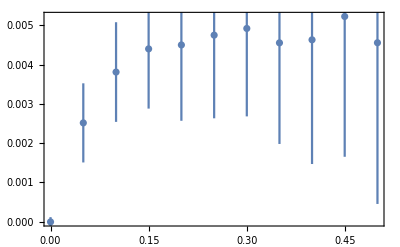

```mathematica
ErrorListPlot[
te`data`ge`light`bar,
AxesOrigin->{0,0},
PlotRange->{Full,Full},
PlotRangePadding->{Automatic,Scaled[.3]},
ImageSize->Scaled[0.4],
AspectRatio->1/GoldenRatio,
Frame->True
]
```

nucleon`gm`lightsea

```mathematica
te`data`lightsea=Table[
{
{Mean[te`data`negative⟦ii;;ii+2,1⟧],
1/4(2*Median[te`data`negative⟦ii;;ii+2,2⟧]+Max[te`data`negative⟦ii;;ii+2,2⟧]+Min[te`data`negative⟦ii;;ii+2,2⟧])
},
1/2(Max[te`data`negative⟦ii;;ii+2,2⟧]-Min[te`data`negative⟦ii;;ii+2,2⟧])
}
,{ii,1,Length[te`data`negative],3}
]
```

Part::take: 无法在 SortBy[$Failed,First] 中提取位置 1 至 3.

General::stop: 在本次计算中，Part::take 的进一步输出将被抑制.

{{{Mean[SortBy[$Failed,First]⟦1;;3,1⟧],1/4 (2 Median[SortBy[$Failed,First]⟦1;;3,2⟧]+2 SortBy[$Failed,First]⟦1;;3,2⟧)},0}}

```mathematica
te`data`lightsea`bar=MapAt[ErrorBar,te`data`lightsea,{;;,2}]
```

{{{Mean[SortBy[$Failed,First]⟦1;;3,1⟧],1/4 (2 Median[SortBy[$Failed,First]⟦1;;3,2⟧]+2 SortBy[$Failed,First]⟦1;;3,2⟧)},ErrorBar[0]}}

```mathematica
ErrorListPlot[
te`data`lightsea`bar,
AxesOrigin->{0,0},
PlotRange->{Full,Full},
PlotRangePadding->{Automatic,Scaled[.3]},
ImageSize->Scaled[0.4],
AspectRatio->1/GoldenRatio,
Frame->True
]
```

-Graphics-